```mathematica
RandomVariate[BinormalDistribution[.75],10]
```

{{-0.674821,-0.858202},{-0.607121,-0.486516},{1.05984,0.495854},{0.205857,-0.796952},{1.925,2.10799},{-2.13251,-1.359},{-0.842391,-0.301896},{-0.532291,-0.514975},{-0.314874,-0.00693088},{-1.85314,-1.5006}}

```mathematica
ClearAll
```

```mathematica
Clear[x]
```

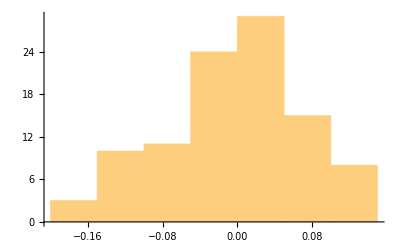

```mathematica
Histogram[Table[Part[First[Correlation[RandomVariate[BinormalDistribution[0],200]]],2],{100}]]
```

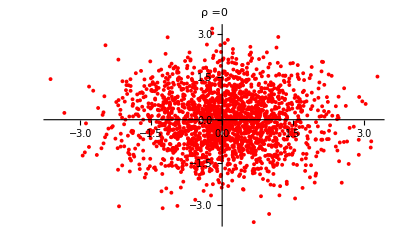
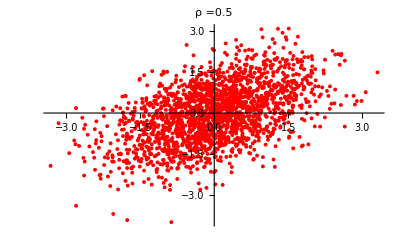
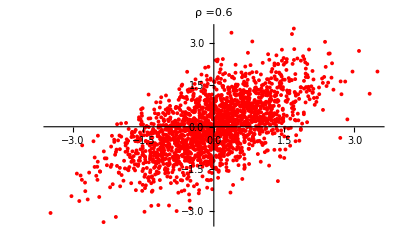
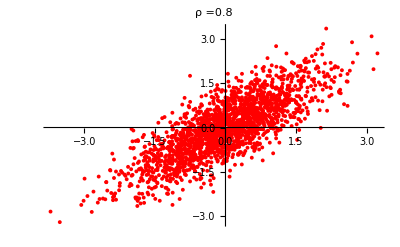
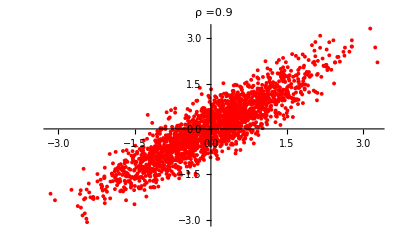
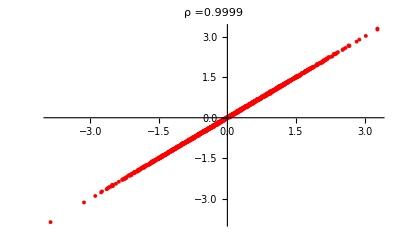

```mathematica
Table[ListPlot[RandomVariate[BinormalDistribution[ρ],2000],PlotStyle->Red,PlotLabel->Row[{"ρ =",ρ}]],{ρ,{0,0.5,0.6,0.8,0.9,0.9999}}]
```

```mathematica
f= PDF[BinormalDistribution[ρ],{x,y}]
```

```mathematica
g= FullSimplify[PowerExpand[PDF[BinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{Subscript[σ, 1],Subscript[σ, 2]} ,ρ],{x,y}]]]
```

(ⅇ^(((y-μ_2)^2+((x-μ_1) σ_2 (2 ρ (-y+μ_2) σ_1+(x-μ_1) σ_2))/σ_1^2)/(2 (-1+ρ^2) σ_2^2)))/(2 π √(1-ρ^2) σ_1 σ_2)

```mathematica
A={Subscript[σ, 1]>0, Subscript[σ, 2]>0,0<ρ<1};
res0=PowerExpand[FullSimplify[Integrate[x*g,{x,-∞,∞},Assumptions->A]/Integrate[g,{x,-∞,∞},Assumptions->A]]]
```

μ_1+(ρ (y-μ_2) σ_1)/σ_2

```mathematica
res1=FullSimplify[PowerExpand[Integrate[(x-res0)^2 g,{x,-∞,∞},Assumptions->A],Assumptions->A]]/FullSimplify[PowerExpand[Integrate[g,{x,-∞,∞},Assumptions->A],Assumptions->A]]
```

(ⅈ (-1+ρ^2)^(3/2) σ_1^2)/(√(1-ρ^2))

```mathematica
FullSimplify[(ⅈ (-1+ρ^2)^(3/2) Subscript[σ, 1]^2)/(√(1-ρ^2)),1>ρ>0]
```

-(-1+ρ^2) σ_1^2

```mathematica
X:= RandomVariate[NormalDistribution[],10^3];
Y:= Table[If[X[[i]]<0,X[[i]],-X[[i]]],{i,1,Length[X]}];
```

```mathematica
Z:= SmoothKernelDistribution[Transpose[{X,Y}],0.03,"Gaussian"];
Dx = SmoothKernelDistribution[X,0.03, "Gaussian"];
Dy = SmoothKernelDistribution[X,0.03, "Gaussian"];
```

```mathematica
Correlation[X,Y]
```

0.0178276

```mathematica
MI := ∫_(-∞)^∞ ∫_(-∞)^∞ PDF[Z,{x,y}]Log[Max[PDF[Z,{x,y}],10^8]/(Max[PDF[Dx,{x,y}],10^-8]Max[PDF[Dy,{x,y}],10^-8])]ⅆxⅆy
```

```mathematica
Equivalent Correlation (in other words, converting MI into a single equivalent corrletion)
```

```mathematica
ρ:= ±√(1-ⅇ^(-2MI))
```